```mathematica
FromEmptyToComplete=ConversionMatrix["E","C"];
```

```mathematica
Fold[And,Monitor[Table[BaseCoeff[k,"E"].FromEmptyToComplete==BaseCoeff[k,"C"],{k,Sort[Keys[allGraphs5]]}],k]]
```

True

```mathematica
With[{from="C",to="E"},
With[{
mat=ConversionMatrix[from,to]},
Fold[And,Monitor[Table[BaseCoeff[k,from].mat==BaseCoeff[k,to],{k,Sort[Keys[allGraphs5]]}],k]]
]
]
```

True

```mathematica
Table[
With[{
mat=ConversionMatrix[from,to]},
Fold[And,Monitor[Table[BaseCoeff[k,from].mat==BaseCoeff[k,to],{k,Sort[Keys[allGraphs5]]}],{k,from->to}]]
]
,{from,allBases}  ,{to,allBases  }
]
```

{{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True}}

```mathematica
With[{
mat=ConversionMatrix[from,to]},
Fold[And,Monitor[Table[BaseCoeff[k,from].mat==BaseCoeff[k,to],{k,Sort[Keys[allGraphs5]]}],k]]
]
```

## Now some equations

```mathematica
VecEqual[v1_,v2_]:=Fold[And,Table[v1[[k]]==v2[[k]],{k,Length[v1]}]]
```

```mathematica
{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4}
```

```mathematica
With[{from="E",to="C"},
With[{
mat=ConversionMatrix[from,to],
vecFrom=Table[v,{v,Bases[from,"Variables"]}],
vecTo=Table[v,{v,Bases[to,"Variables"]}],
nullTo=Select[Bases[to,"Variables"],StringCount[SymbolName[#],"x"]≤2&],
notnullTo=Select[Bases[to,"Variables"],StringCount[SymbolName[#],"x"]>2&],
varFrom=Bases[from,"Variables"],
varFromTop=Select[Bases[from,"Variables"],StringCount[SymbolName[#],"x"]>2&]
},
Reduce[
Eliminate[Simplify[VecEqual[vecFrom.mat,vecTo] && Fold[And,Map[#==0&,nullTo]]],Bases[to,"Variables"]],
varFromTop
]
]
]//ExpressionToTable
```

n1x2345==-2 (n1x23x45+n1x24x35+n1x25x34)
n1345x2==-2 (n13x2x45+n14x2x35+n15x2x34)
n15x234+2 n15x2x34+n1x23x45+n1x24x35==n1x2x345
n14x235+2 n14x2x35+n1x23x45+n1x25x34==n1x2x345
n13x245+2 n13x2x45+n1x24x35+n1x25x34==n1x2x345
n1x234x5+n1x2x345+2 n1x2x34x5==n1x23x45+n1x24x35
n1x245x3+n1x2x345+2 n1x2x3x45==n1x24x35+n1x25x34
n12x345+2 n12x3x45+n1x24x35+n1x25x34==n1x245x3
n1x235x4+n1x2x345+2 n1x2x35x4==n1x23x45+n1x25x34
n145x23+n14x2x35+n15x2x34+2 n1x23x45==n1x2x345
n135x24+n13x2x45+n15x2x34+2 n1x24x35==n1x2x345
n134x25+n13x2x45+n14x2x35+2 n1x25x34==n1x2x345
n1x235x4+n1x245x3+2 n1x25x3x4==n1x23x45+n1x24x35
n1x234x5+n1x245x3+2 n1x24x3x5==n1x23x45+n1x25x34
n1x234x5+n1x235x4+2 n1x23x4x5==n1x24x35+n1x25x34
n145x2x3+n1x24x35+n1x25x34==n14x2x35+n15x2x34+n1x245x3
n135x2x4+n1x23x45+n1x25x34==n13x2x45+n15x2x34+n1x235x4
n134x2x5+n1x23x45+n1x24x35==n13x2x45+n14x2x35+n1x234x5
2 n15x23x4+n1x25x34+n1x2x345==2 n15x2x34+n1x235x4+n1x23x45
2 n14x23x5+n1x24x35+n1x2x345==2 n14x2x35+n1x234x5+n1x23x45
2 n15x24x3+n1x25x34+n1x2x345==2 n15x2x34+n1x245x3+n1x24x35
2 n13x24x5+n1x23x45+n1x2x345==2 n13x2x45+n1x234x5+n1x24x35
2 n14x25x3+n1x24x35+n1x2x345==2 n14x2x35+n1x245x3+n1x25x34
n1245x3==-2 (n12x3x45+n14x2x35+n15x2x34+n1x245x3-n1x2x345)
2 n13x25x4+n1x23x45+n1x2x345==2 n13x2x45+n1x235x4+n1x25x34
2 n12x34x5+n1x23x45+n1x245x3==2 n12x3x45+n1x234x5+n1x25x34
2 n12x35x4+n1x23x45+n1x245x3==2 n12x3x45+n1x235x4+n1x24x35
2 n125x34+2 n12x3x45+2 n15x2x34+n1x24x35+3 n1x25x34==n1x245x3+n1x2x345
2 n124x35+2 n12x3x45+2 n14x2x35+3 n1x24x35+n1x25x34==n1x245x3+n1x2x345
2 n15x2x34+2 n15x2x3x4+n1x235x4+n1x245x3==n1x23x45+n1x24x35+2 n1x25x34
2 n14x2x35+2 n14x2x3x5+n1x234x5+n1x245x3==n1x23x45+2 n1x24x35+n1x25x34
2 n13x2x45+2 n13x2x4x5+n1x234x5+n1x235x4==2 n1x23x45+n1x24x35+n1x25x34
2 n12x3x45+2 n12x3x4x5+n1x234x5+n1x235x4==2 n1x23x45+n1x24x35+n1x25x34
n1x234x5+n1x235x4+n1x245x3+n1x2x345==2 (n1x23x45+n1x24x35+n1x25x34+n1x2x3x4x5)
2 n123x45+2 n12x3x45+2 n13x2x45+2 n1x23x45+n1x24x35+n1x25x34==n1x245x3+n1x2x345
2 n125x3x4+2 n1x23x45+n1x24x35+n1x25x34+n1x2x345==2 n12x3x45+2 n15x2x34+2 n1x235x4+n1x245x3
2 n124x3x5+2 n1x23x45+n1x24x35+n1x25x34+n1x2x345==2 n12x3x45+2 n14x2x35+2 n1x234x5+n1x245x3
n1234x5+2 n12x3x45+2 n13x2x45+2 n14x2x35+3 n1x234x5+n1x25x34==n1x23x45+n1x245x3+2 n1x2x345
n1235x4+2 n12x3x45+2 n13x2x45+2 n15x2x34+3 n1x235x4+n1x24x35==n1x23x45+n1x245x3+2 n1x2x345
n12345+3 n1x245x3+9 n1x2x345==6 n12x3x45+6 n13x2x45+6 n14x2x35+6 n15x2x34+6 n1x23x45+9 n1x24x35+9 n1x25x34
1/2 (2 n123x4x5+2 n1x23x45+n1x245x3+n1x24x35+n1x25x34+n1x2x345)==n12x3x45+n13x2x45+n1x234x5+n1x235x4

```mathematica
With[{from="F",to="C"},
With[{
mat=ConversionMatrix[from,to],
vecFrom=Table[v,{v,Bases[from,"Variables"]}],
vecTo=Table[v,{v,Bases[to,"Variables"]}],
nullTo=Select[Bases[to,"Variables"],StringCount[SymbolName[#],"x"]≤2&],
notnullTo=Select[Bases[to,"Variables"],StringCount[SymbolName[#],"x"]>2&],
varFrom=Bases[from,"Variables"],
varFromTop=Select[Bases[from,"Variables"],StringCount[SymbolName[#],"x"]>2&],
varFromTop2=Select[Bases[from,"Variables"],StringCount[SymbolName[#],"x"]==3&]
},
Reduce[
Eliminate[Simplify[VecEqual[vecFrom.mat,vecTo] && Fold[And,Map[#==0&,nullTo]]],Bases[to,"Variables"]],
varFromTop
]
]
]//ExpressionToTable2
```

p1x2x3x4x5==0
p14x235==-(3 p1x235x4)/2
p13x245==-(3 p1x245x3)/2
p12x345==-(3 p1x2x345)/2
p12x3x4x5+p1x2x345==0
p14x2x3x5+p1x235x4==0
p13x2x4x5+p1x245x3==0
p1x23x45+p1x24x35+p1x25x34==0
2 p15x234==3 (p1x235x4+p1x245x3+p1x2x345)
2 p134x2x5==p1x235x4+p1x245x3+2 p1x25x34
2 p135x2x4+p1x235x4+p1x2x345==2 p1x24x35
p15x2x3x4==p1x235x4+p1x245x3+p1x2x345
2 (p1x24x35+p1x24x3x5)==p1x235x4+p1x2x345
2 p124x3x5==p1x235x4+2 p1x24x35+p1x2x345
p1x234x5+p1x235x4+p1x245x3+p1x2x345==0
p1x235x4+2 p1x24x35+p1x2x345+2 p1x2x35x4==0
4 p12x35x4==p1x235x4+2 p1x24x35+3 p1x2x345
4 p135x24==3 (p1x235x4-2 p1x24x35+p1x2x345)
4 p14x2x35==3 p1x235x4+2 p1x24x35+p1x2x345
p124x35==-3/4 (p1x235x4+2 p1x24x35+p1x2x345)
p1x235x4+p1x245x3+2 (p1x25x34+p1x25x3x4)==0
2 p125x3x4+p1x235x4+p1x245x3==2 p1x25x34
p1x235x4+p1x245x3==2 (p1x25x34+p1x2x34x5)
4 p14x25x3==3 p1x235x4+p1x245x3+2 p1x25x34
4 p13x25x4==p1x235x4+3 p1x245x3+2 p1x25x34
p134x25==-3/4 (p1x235x4+p1x245x3+2 p1x25x34)
4 p125x34==3 (p1x235x4+p1x245x3-2 p1x25x34)
2 p145x2x3+p1x245x3+2 p1x24x35+2 p1x25x34+p1x2x345==0
4 p15x24x3+3 p1x235x4+2 p1x245x3+3 p1x2x345==2 p1x24x35
4 p12x34x5+p1x235x4+p1x245x3==2 (p1x25x34+p1x2x345)
4 p13x24x5+p1x235x4+p1x2x345==2 (p1x245x3+p1x24x35)
2 (p123x4x5+p1x24x35+p1x25x34)==p1x245x3+p1x2x345
2 p1x23x4x5==p1x245x3+2 p1x24x35+2 p1x25x34+p1x2x345
4 p15x2x34+3 p1x235x4+3 p1x245x3+2 p1x2x345==2 p1x25x34
4 p145x23==3 (p1x245x3+2 p1x24x35+2 p1x25x34+p1x2x345)
2 (2 p13x2x45+p1x24x35+p1x25x34)==3 p1x245x3+p1x2x345
2 (2 p12x3x45+p1x24x35+p1x25x34)==p1x245x3+3 p1x2x345
2 (p1x24x35+p1x25x34)==p1x245x3+p1x2x345+2 p1x2x3x45
p123x45==-3/4 (p1x245x3-2 p1x24x35-2 p1x25x34+p1x2x345)
4 p15x23x4+2 p1x235x4+3 p1x245x3+2 p1x24x35+2 p1x25x34+3 p1x2x345==0
4 p14x23x5+p1x245x3+2 p1x24x35+2 p1x25x34+p1x2x345==2 p1x235x4

```mathematica
With[{from="G",to="C"},
With[{
mat=ConversionMatrix[from,to],
vecFrom=Table[v,{v,Bases[from,"Variables"]}],
vecTo=Table[v,{v,Bases[to,"Variables"]}],
nullTo=Select[Bases[to,"Variables"],StringCount[SymbolName[#],"x"]≤2&],
notnullTo=Select[Bases[to,"Variables"],StringCount[SymbolName[#],"x"]>2&],
varFrom=Bases[from,"Variables"],
varFromTop=Select[Bases[from,"Variables"],StringCount[SymbolName[#],"x"]>2&]
},
Eliminate[Simplify[VecEqual[vecFrom.mat,vecTo] && Fold[And,Map[#==0&,nullTo]]],Bases[to,"Variables"]]
]
]
```

g12345==0&&g1234x5==0&&g1235x4==0&&g123x45==0&&g123x4x5==0&&g1245x3==0&&g124x35==0&&g124x3x5==0&&g125x34==0&&g125x3x4==0&&g12x345==0&&g12x34x5==0&&g12x35x4==0&&g12x3x45==0&&g1345x2==0&&g134x25==0&&g134x2x5==0&&g135x24==0&&g135x2x4==0&&g13x245==0&&g13x24x5==0&&g13x25x4==0&&g13x2x45==0&&g145x23==0&&g145x2x3==0&&g14x235==0&&g14x23x5==0&&g14x25x3==0&&g14x2x35==0&&g15x234==0&&g15x23x4==0&&g15x24x3==0&&g15x2x34==0&&g1x2345==0&&g1x234x5==0&&g1x235x4==0&&g1x23x45==0&&g1x245x3==0&&g1x24x35==0&&g1x25x34==0&&g1x2x345==0

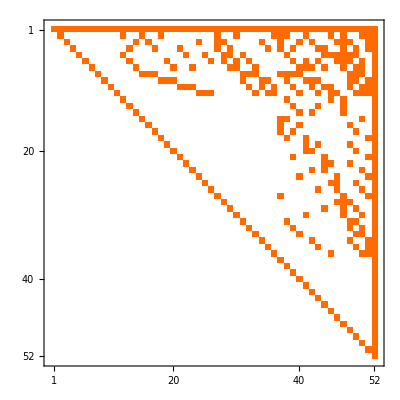

```mathematica
MatrixPlot[ConversionMatrix["E","C"]]
```

```mathematica
Det[ConversionMatrix["E","C"]]
```

1

```mathematica
Det[ConversionMatrix["C","F"]]
```

-1/195689447424

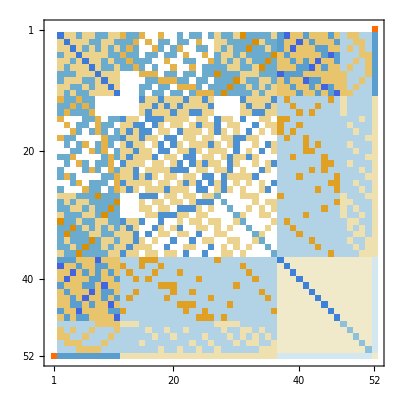

```mathematica
MatrixPlot[Inverse[ConversionMatrix["F","C"]]]
```

```mathematica
MatrixForm[Table[i+j,{i,0,20},{j,0,20}]]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31
12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32
13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33
14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34
15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37
18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38
19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40)